```mathematica
xd={{-1},{2}}
sd={{2,1},{1,3}}
x={{x1},{x2}}
n1=20
n2=30
p=2
c=Sqrt[p(n1+n2-2)/(n1+n2-p-1)*InverseCDF[FRatioDistribution[p,n1+n2-p-1],0.95]]
```

{{-1},{2}}

{{2,1},{1,3}}

{{x1},{x2}}

20

30

2

2.55462

```mathematica
t2=Simplify[(Transpose[xd-x].Inverse[(1/n1+1/n2)sd].(xd-x))[[1,1]]]
```

12/5 (15+3 x1^2-2 x1 (-5+x2)-10 x2+2 x2^2)

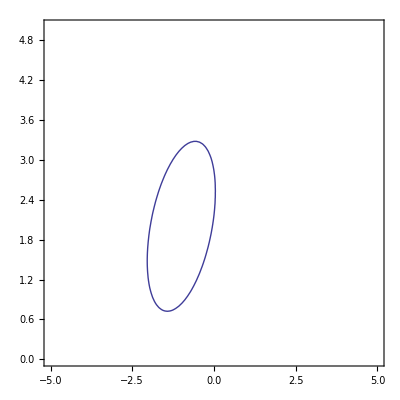

```mathematica
ContourPlot[t2==c^2,{x1,-5,5},{x2,0,5}]
```